# Problema 3.9

## Datos

```mathematica
(*in*)
```

```mathematica
d2=1;
d3=3.5;(*MODIFICADO*)
d3p=3.5;(*MODIFICADO*)
d4=4;(*Modificado*)
d6=4.6; (*Recordar que todas son ctes*)
```

## Ecuaciones cinemáticas

```mathematica
Clear[θ2,θ3,θ4,x5,θ6]
Clear[ω2,ω3,ω4,vx5,ω6]
Clear[α2,α3,α4,ax5,α6]
```

### Ecuaciones de Posición

```mathematica
(*Recordar que θ y β se tienen que sumar*)
u2={Cos[θ2], Sin[θ2],0};
u3={Cos[θ3],Sin[θ3],0};
u4={Cos[θ4],Sin[θ4],0};
u5={Cos[θ3+(105*Degree)],Sin[θ3+(105*Degree)],0};
u6={Cos[θ6],Sin[θ6],0};

R1={0,3,0};
R1p={-5.6,2.65,0};
R2=d2*u2;
R3=d3*u3;
R3p=d3p*u3;
R4=d4*u4;
R5=x5*u5;
R6=d6*u6;

(*Lazos vectoriales*)

pos1=R2+R3p-R4-R1;
pos2=R2+R3+R5-R6-R1p;
```

### Ecuaciones de Velocidad

```mathematica
omega2={0,0,ω2};
omega3={0,0,ω3};
omega4={0,0,ω4};
omega6={0,0,ω6};

(*V1 y V1P = NULOS*)
V2=omega2×R2;
V3=omega3×R3;
V3p=omega3×R3p;
V4 = omega4×R4;
V5=vx5*u5+omega3×R5; (*CASO 3*)
V6=omega6×R6;

(*Lazos vectoriales *)

vel1=V2+V3p-V4;
vel2=V2+V3+V5-V6;
```

### Ecuaciones de Aceleración

```mathematica
alfa2={0,0,α2};
alfa3={0,0,α3};
alfa4={0,0,α4};
alfa6={0,0,α6};

A2=alfa2×R2-ω2^2*R2;
A3=alfa3×R3-ω3^2*R3;
A3p=alfa3×R3p-ω3^2*R3p;
A4=alfa4×R4-ω4^2*R4;
A5=ax5*u5+2omega3×(vx5*u5)+alfa3×R5-ω3^2*R5;(*CASO 3*)
A6=alfa6×R6-ω6^2*R6;

(*Lazos vectoriales *)

acel1=A2+A3p-A4;
acel2=A2+A3+A5-A6;
```

## Solución de Posición

### Solución Inicial

```mathematica
Clear[θ2,θ3,θ4,x5,θ6]
Clear[ω2,ω3,ω4,vx5,ω6]
Clear[α2,α3,α4,ax5,α6]

θ2=100*Degree; (*Variable de control*)

SolInicial = FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0}, 
{{θ3,145*Degree},
{θ4,180*Degree},
{x5,2.5},
{θ6,275*Degree}},MaxIterations->15]
```

{θ3→3.03154,θ4→3.56152,x5→2.70121,θ6→5.25006}

### Solución Total

```mathematica
Clear[θ2,θ3,θ4,x5,θ6]
Clear[ω2,ω3,ω4,vx5,ω6]
Clear[α2,α3,α4,ax5,α6]

(*Declarando mis variables iniciales*)

θ3i=θ3/.SolInicial;
θ4i=θ4/.SolInicial;
x5i=x5/.SolInicial;
θ6i=θ6/.SolInicial;

For[i = 100,i≤460, i+=1,
θ2 = i*Degree;
SolPos[i]= FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0}, 
{{θ3, θ3i},
{θ4,θ4i},
{x5,x5i},
{θ6, θ6i}},MaxIterations->15];
θ3i=θ3/.SolPos[i];
θ4i=θ4/.SolPos[i];
x5i=x5/.SolPos[i];
θ6i=θ6/.SolPos[i];]
```

## Gráficas de Posición

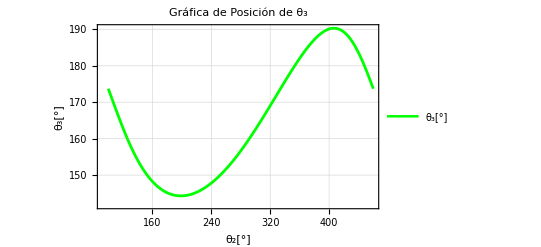

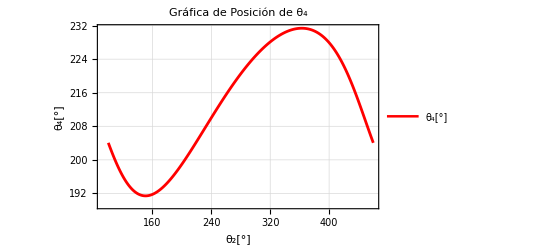

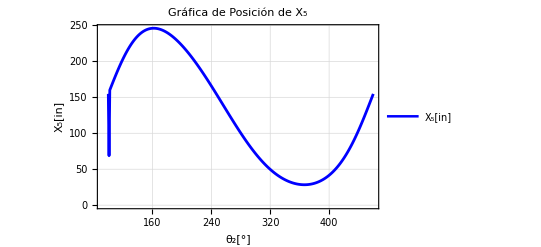

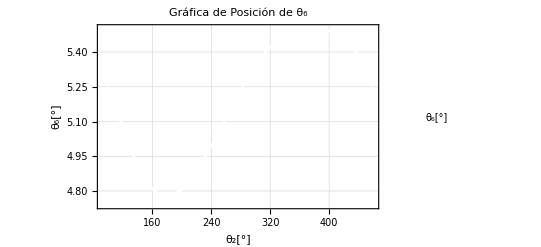

```mathematica
tabla1 = Table[{i,(θ3/.SolPos[i])/Degree},{i,100,460,1}];
tabla2 = Table[{i,(θ4/.SolPos[i])/Degree},{i,100,460,1}];
tabla3 = Table[{i,(x5/.SolPos[i])/Degree},{i,100,460,1}];
tabla4 = Table[{i,θ6/.SolPos[i]},{i,100,460,1}];

ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ_2[°]","θ_3[°]"},
PlotLabel->"Gráfica de Posición de θ_3",
PlotLegends->{"θ_3[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ_2[°]","θ_4[°]"},
PlotLabel->"Gráfica de Posición de θ_4",
PlotLegends->{"θ_4[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]

ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ_2[°]","X_5[in]"},
PlotLabel->"Gráfica de Posición de X_5",
PlotLegends->{"X_5[in]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]

ListPlot[tabla4,
Frame->True,
FrameLabel->{"θ_2[°]","θ_6[°]"},
PlotLabel->"Gráfica de Posición de θ_6",
PlotLegends->{"θ_6[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Solución de Velocidad

```mathematica
Clear[θ2,θ3,θ4,x5,θ6]
Clear[ω2,ω3,ω4,vx5,ω6]
Clear[α2,α3,α4,ax5,α6]

ω2=10; 

(*Vuelta completa*)
For[i = 100,i≤460, i+=1,
θ2 = i*Degree;

SolVel[i]= Solve[{
vel1⟦1⟧==0,
vel1⟦2⟧==0,
vel2⟦1⟧==0,
vel2⟦2⟧==0}/.SolPos[i],
{ω3,ω4,vx5,ω6}]//Flatten;];
```

## Gráficas de Velocidad

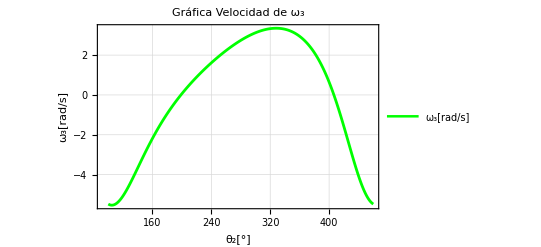

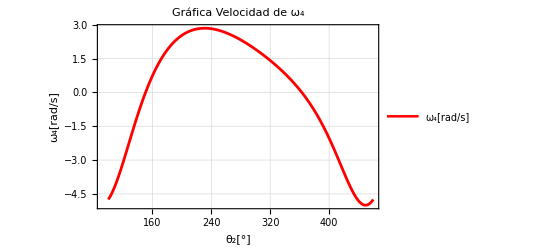

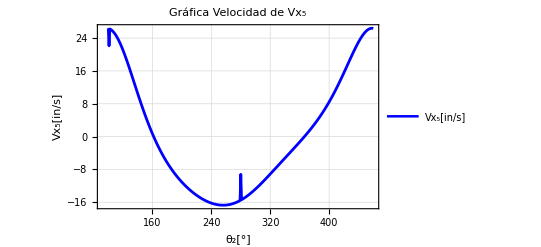

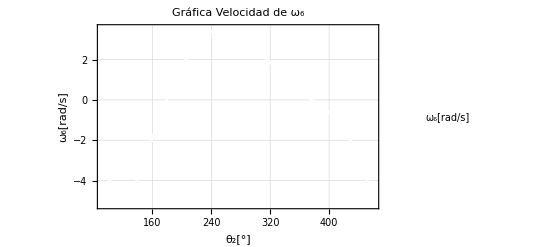

```mathematica
tabla5 = Table[{i,ω3/.SolVel[i]},{i,100,460,1}];
tabla6 = Table[{i,ω4/.SolVel[i]},{i,100,460,1}];
tabla7 = Table[{i,vx5/.SolVel[i]},{i,100,460,1}];
tabla8 = Table[{i,ω6/.SolVel[i]},{i,100,460,1}];

ListPlot[tabla5,
Frame->True,
FrameLabel->{"θ_2[°]","ω_3[rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_3",
PlotLegends->{"ω_3[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla6,
Frame->True,
FrameLabel->{"θ_2[°]","ω_4[rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_4",
PlotLegends->{"ω_4[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]

ListPlot[tabla7,
Frame->True,
FrameLabel->{"θ_2[°]","Vx_5[in/s]"},
PlotLabel->"Gráfica Velocidad de Vx_5",
PlotLegends->{"Vx_5[in/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]

ListPlot[tabla8,
Frame->True,
FrameLabel->{"θ_2[°]","ω_6[rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_6",
PlotLegends->{"ω_6[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Solución de Aceleración

```mathematica
Clear[θ2,θ3,θ4,x5,θ6]
Clear[ω2,ω3,ω4,vx5,ω6]
Clear[α2,α3,α4,ax5,α6]
ω2=10; 
α2=-1; 

For[i = 100,i≤460, i+=1,

θ2 = i*Degree;

SolAcel[i]= Solve[{
acel1⟦1⟧==0,
acel1⟦2⟧==0,
acel2⟦1⟧==0,
acel2⟦2⟧==0}/.SolVel[i]/.SolPos[i] ,
{α3,α4,ax5,α6}]//Flatten;];
```

## Gráfica de Aceleración

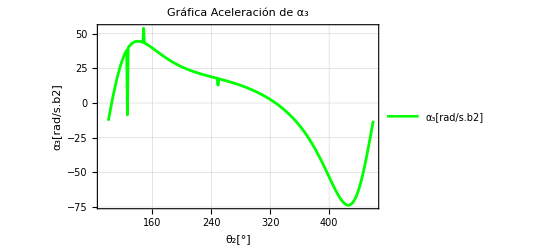

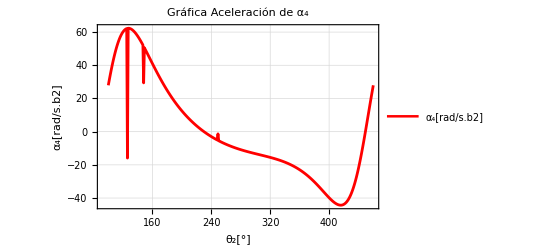

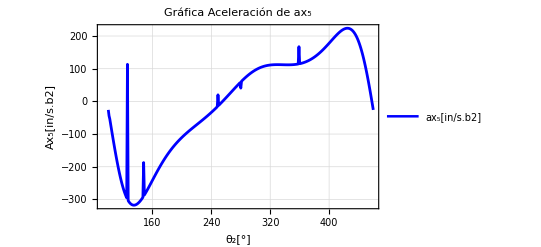

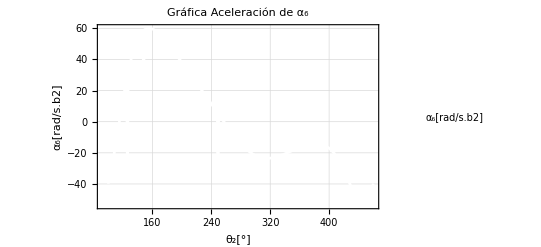

```mathematica
tabla9= Table[{i,α3/.SolAcel[i]},{i,100,460,1}];
tabla10= Table[{i,α4/.SolAcel[i]},{i,100,460,1}];
tabla11= Table[{i,ax5/.SolAcel[i]},{i,100,460,1}];
tabla12= Table[{i,α6/.SolAcel[i]},{i,100,460,1}];

ListPlot[tabla9,
Frame->True,
FrameLabel->{"θ_2[°]","α_3[rad/s.b2]"},
PlotLabel->"Gráfica Aceleración de α_3",
PlotLegends->{"α_3[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla10,
Frame->True,
FrameLabel->{"θ_2[°]","α_4[rad/s.b2]"},
PlotLabel->"Gráfica Aceleración de α_4",
PlotLegends->{"α_4[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]

ListPlot[tabla11,
Frame->True,
FrameLabel->{"θ_2[°]","Ax_5[in/s.b2]"},
PlotLabel->"Gráfica Aceleración de ax_5",
PlotLegends->{"ax_5[in/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]

ListPlot[tabla12,
Frame->True,
FrameLabel->{"θ_2[°]","α_6[rad/s.b2]"},
PlotLabel->"Gráfica Aceleración de α_6",
PlotLegends->{"α_6[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Simulación

```mathematica
Clear[θ2,θ3,θ4,x5,θ6]

Animate[

θ2 = i*Degree;

x={1,0,0};
y={0,1,0};
k={0,0,1};

cero={0,0,0};

(*-----DEFINIENDO GEOMETRICAMENTE-----*)

eslabon2=Cylinder[{cero,R2},0.1];
eslabon3a=Cylinder[{R2+0.4*k,R2+R3+0.4*k},0.1]/.SolPos[i];
eslabon3b=Cylinder[{R2+R3+0.4*k,R2+R3+R3p+0.4*k},0.1]/.SolPos[i];
eslabon4=Cylinder[{cero+3*y+0.6*k,R2+R3+R3p+0.6*k},0.1]/.SolPos[i];
eslabon5=Cylinder[{R2+R3+0.4*k,R2+R3+6*u5+0.4*k},0.1]/.SolPos[i];
eslabon5a=Cylinder[{R2+R3+R5+0.2*y+0.4*k,R2+R3+R5-0.2*y+0.4*k},0.3]/.SolPos[i];
eslabon6=Cylinder[{R1p,R1p+R6},0.1]/.SolPos[i];


ejeT=Cylinder[{cero-0.2*k,0.2*k},0.15];
ejeA=Cylinder[{R2-0.2*k,R2+0.8*k},0.15];
ejeC=Cylinder[{R2+R3-0.1*k,R2+R3+0.8*k},0.15]/.SolPos[i];
ejeD=Cylinder[{R2+R3+R3p+0.2*k,R2+R3+R3p+0.8*k},0.15]/.SolPos[i];
ejeF=Cylinder[{R2+R3+R5+0.2*k,R2+R3+R5+0.8*k},0.15]/.SolPos[i];
(*-----CARACTERISTICAS-----*)

barra2=Graphics3D[{Purple,eslabon2}];
barra3a=Graphics3D[{Red,eslabon3a}];
barra3b=Graphics3D[{Red,eslabon3b}];
barra4=Graphics3D[{Green,eslabon4}];
barra5=Graphics3D[{Pink,eslabon5}];
corredera6=Graphics3D[{Yellow,eslabon5a}];
barra6=Graphics3D[{Pink,eslabon6}];

pernoT=Graphics3D[{Black,ejeT}];
pernoA=Graphics3D[{Black,ejeA}];
pernoC=Graphics3D[{Black,ejeC}];
pernoD=Graphics3D[{Black,ejeD}];
pernoF=Graphics3D[{Black,ejeF}];
Show[barra2,barra3a,barra3b,barra4,barra5,corredera6,barra6,pernoT,pernoA,pernoC,pernoD,pernoF,
Axes->True,
AspectRatio->1,
AxesLabel->{"X [in]","Y [in]","Z [in]"},
ImageSize->400,
ViewVertical->{0,1,0},
ViewPoint->{0,0,Infinity},
PlotRange->{{-10,10},{-5,7},{-1,1.3}}
],{i,180,460,1},AnimationRunning->False]
```